## One TLS connected to two thermal baths with different temperatures

Working in natural units.
Thermal baths are bosonic and Ohmic.

```mathematica
unitassum={ℏ->1,k->1};
NBEassum=Subscript[NBE, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
Jassum=Subscript[J, P_][ω_]->Subscript[κ, P] ω;
```

### Density matrix

```mathematica
ρMatrix=({{Subscript[ρ, 1,1], Subscript[ρ, 1,2]}, {Subscript[ρ, 2,1], Subscript[ρ, 2,2]}});
```

### System Hamiltonian

```mathematica
Hs = (ℏ ω)/2({{1, 0}, {0, -1}});
```

### Get projection matrices Π(ϵ)

```mathematica
πMatrix[1]=({{1, 0}, {0, 0}});
πMatrix[2]=({{0, 0}, {0, 1}});
```

### Get Lindblad operators A^P(ω)

Only a single Lindblad operator exists.

```mathematica
AMatrix[ω]=πMatrix[2].({{0, 1}, {1, 0}}).πMatrix[1];
%//MatrixForm
```

(0 | 0
1 | 0)

### Calculate Lindbladian terms

```mathematica
Subscript[LinMatrix, P_][ρ_]:=(Subscript[J, P][ω](1+Subscript[NBE, P][ω])(AMatrix[ω].ρ.AMatrix[ω]†-1/2(AMatrix[ω]†.AMatrix[ω].ρ+ρ.AMatrix[ω]†.AMatrix[ω]))+Subscript[J, P][ω]Subscript[NBE, P][ω](AMatrix[ω]†.ρ.AMatrix[ω]-1/2(AMatrix[ω].AMatrix[ω]†.ρ+ρ.AMatrix[ω].AMatrix[ω]†)))
```

```mathematica
Simplify[Subscript[LinMatrix, 1][ρMatrix]]//MatrixForm
Simplify[Subscript[LinMatrix, 2][ρMatrix]]//MatrixForm
```

(J_1[ω] (ρ_(2,2) NBE_1[ω]-ρ_(1,1) (1+NBE_1[ω])) | -1/2 ρ_(1,2) J_1[ω] (1+2 NBE_1[ω])
-1/2 ρ_(2,1) J_1[ω] (1+2 NBE_1[ω]) | J_1[ω] (-ρ_(2,2) NBE_1[ω]+ρ_(1,1) (1+NBE_1[ω])))

(J_2[ω] (ρ_(2,2) NBE_2[ω]-ρ_(1,1) (1+NBE_2[ω])) | -1/2 ρ_(1,2) J_2[ω] (1+2 NBE_2[ω])
-1/2 ρ_(2,1) J_2[ω] (1+2 NBE_2[ω]) | J_2[ω] (-ρ_(2,2) NBE_2[ω]+ρ_(1,1) (1+NBE_2[ω])))

### Solve the master equation for a stationary state

```mathematica
sol = Flatten[Solve[{({{0, 0}, {0, 0}})== Subscript[LinMatrix, 1][ρMatrix]+Subscript[LinMatrix, 2][ρMatrix],Subscript[ρ, 1,1]+Subscript[ρ, 2,2]==1},{Subscript[ρ, 1,1],Subscript[ρ, 1,2],Subscript[ρ, 2,1],Subscript[ρ, 2,2]}]];
statstate=Simplify[ρMatrix//.Flatten[{sol,NBEassum,unitassum,Jassum}]];
MatrixForm[statstate//.{Subscript[T, 1]->TL,Subscript[T, 2]->TR,Subscript[κ, 1]->κL,Subscript[κ, 2]->κR}]
```

(((-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) κR)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR) | 0
0 | 1-((-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) κR)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR))

```mathematica
DensityMatrix[ω_,TL_,TR_,κL_,κR_]:=({{((-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) κR)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR), 0}, {0, 1-((-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) κR)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR)}})
```

### Energy flow inwards

```mathematica
Subscript[EngyFlowIn, P_][ρ_]:=Simplify[Tr[Subscript[LinMatrix, P][ρ].Hs]]
```

### Energy flows at steady state

```mathematica
Simplify[Subscript[EngyFlowIn, 1][statstate]]
Simplify[Subscript[EngyFlowIn, 1][statstate]//.Flatten[{Jassum,unitassum,NBEassum,Subscript[T, 1]->TL,Subscript[T, 2]->TR,Subscript[κ, 1]->κL,Subscript[κ, 2]->κR}]]
```

(ω ℏ J_1[ω] J_2[ω] (NBE_1[ω]-NBE_2[ω]))/(J_1[ω] (1+2 NBE_1[ω])+J_2[ω] (1+2 NBE_2[ω]))

-((ⅇ^(ω/TL)-ⅇ^(ω/TR)) κL κR ω^2)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR)

At steady state, the rate of heat absorption from the left reservoir,

```mathematica
EnergyFlow[ω_,TL_,TR_,κL_,κR_]:=-((ⅇ^(ω/TL)-ⅇ^(ω/TR)) κL κR ω^2)/((1+ⅇ^(ω/TL)) (-1+ⅇ^(ω/TR)) κL+(-1+ⅇ^(ω/TL)) (1+ⅇ^(ω/TR)) κR)
```

## Example case - Two TLS interconnected through an intermediate bath

We study the following case,
	1. Hot left reservoir at TH = 0.2
	2. Cold right reservoir at TC = 0.02
	3. Two TLS and an intermediate bath with unknown temperature TI in between
	4. All bath couplings are weak at κ = 0.01
	5. Left TLS has ω = 1.0
	6. Right TLS has ω = 0.5
Intermediate bath formalism utilized to calculate TI

Purpose is to get the thermal conductivity of the whole system and afterwards compare it to that of a non-resonant but strongly-coupled two TLS system (in “Two TLSs connected to thermal baths each - Ultrastrong coupling - Global master equation”)

```mathematica
EL=EnergyFlow[1.0,0.2,TI,0.01,0.01];
EI=EnergyFlow[0.5,TI,0.02,0.01,0.01];

TIstat = TI/.FindRoot[EL-EI,{TI,0.02}]
ELstat = EL/.TI->TIstat
```

0.134867

0.0000306782

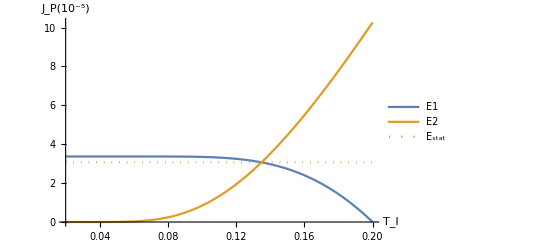

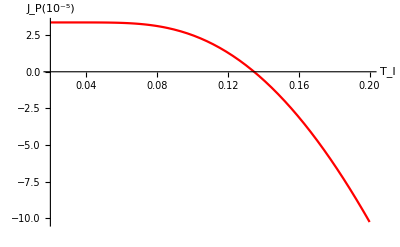

```mathematica
Plot[{10^5 EL,10^5 EI,10^5 ELstat},{TI,0.02,0.2},PlotLegends->{"E1","E2","E_stat"},AxesLabel->{"T_I","J_P(10^-5)"},PlotRange->Full,PlotStyle->{Automatic,Automatic,Dotted}]
Plot[10^5(EL-EI),{TI,0.02,0.2},AxesLabel->{"T_I","J_P(10^-5)"},PlotStyle->Red]
```

We now vary ω2 to see the effect of resonance.

```mathematica
TotEnFlow[TH_,TC_,ω1_,ω2_,κ_]:=Module[{En1,En2,TIstat,ELstat},
En1=EnergyFlow[ω1,TH,TI,κ,κ];
En2=EnergyFlow[ω2,TI,TC,κ,κ];
TIstat = TI/.FindRoot[En1-En2,{TI,TC}];
ELstat = En1/.TI->TIstat
]
```

```mathematica
TotEnFlow[0.2,0.02,1.0,0.5,0.01]
```

0.0000306782

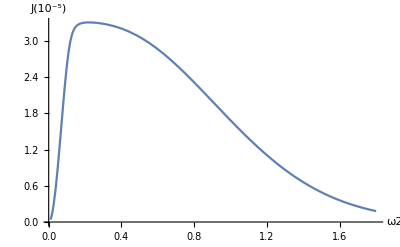

```mathematica
Plot[10^5 TotEnFlow[0.2,0.02,1.0,ω2,0.01],{ω2,0.01,1.8},AxesLabel->{"ω2","J(10^-5)"}]
```